# Algorithmic Differentiation for Cholesky Factorization

## Cholesky Decomposition following Gilles

The Cholesky decomposition factorizes an SPD matrix A as
	A=L.Lᵀ
where L is a lower triangular matrix.  We had code for a Cholesky decomposition.  Differentiating this code would give code for the sensitivities of the the lower triangular factor L.  There is code
         -Graphics-
in the Gilles paper. I am going to implement (and test) that code then differentiate the code.

```mathematica
Chol[AIn_]:= Module[{A=AIn,L=0.0*AIn,m=Length[AIn]},
(* A needs to be SPD *)
Do[
Do[
Do[
A⟦i,j⟧=A⟦i,j⟧-L⟦i,k⟧L⟦j,k⟧,
{k,1,j-1}];
If[i==j,
L⟦i,i⟧=√A⟦i,i⟧,
L⟦i,j⟧=A⟦i,j⟧/L⟦j,j⟧],
{j,1,i}],
{i,1,m}];
L
]
```

As always test.

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ;
L=Chol[A];
{LowerTriangularMatrixQ[L],Norm[A-L.Lᵀ]}
```

{True,4.2682×10^-15}

I am going to differentiate the code.

```mathematica
CholAD[AIn_,dAIn_]:= Module[{A=AIn,dA=dAIn,L=0.0*AIn,dL=0.0*AIn,m=Length[AIn]},
(* A needs to be SPD *)
Do[
Do[
Do[
A⟦i,j⟧=A⟦i,j⟧-L⟦i,k⟧L⟦j,k⟧;
dA⟦i,j⟧=dA⟦i,j⟧-dL⟦i,k⟧L⟦j,k⟧-L⟦i,k⟧dL⟦j,k⟧,
{k,1,j-1}];
If[i==j,
L⟦i,i⟧=√A⟦i,i⟧;dL⟦i,i⟧=0.5dA⟦i,i⟧/√A⟦i,i⟧,
L⟦i,j⟧=A⟦i,j⟧/L⟦j,j⟧; dL⟦i,j⟧=dA⟦i,j⟧/L⟦j,j⟧-A⟦i,j⟧dL⟦j,j⟧/L⟦j,j⟧^2
],
{j,1,i}],
{i,1,m}];
{L,dL}
]
```

As always test.

```mathematica
m=5;
A=RandomReal[{-1,1},{m,m}]; A=A.Aᵀ+IdentityMatrix[m];
dA=RandomReal[{-1,1},{m,m}];dA=(dA + dAᵀ);
(* Test our new code *)
{L,dL}=CholAD[A,dA];
{LowerTriangularMatrixQ[L],Norm[A-L.Lᵀ]}
Map[MatrixForm,{L,dL}]
(* How do we test the "derivative" part of the code? *)
```

{True,4.4869×10^-16}

{(1.79568 | 0. | 0. | 0. | 0.
-0.666061 | 1.47685 | 0. | 0. | 0.
0.199941 | 0.0796636 | 1.43404 | 0. | 0.
0.180152 | 0.346108 | -0.0217532 | 1.28325 | 0.
0.979476 | -0.432802 | -0.194593 | 0.633038 | 1.57727),(-0.169033 | 0. | 0. | 0. | 0.
-0.00925845 | -0.0161779 | 0. | 0. | 0.
0.72256 | 0.00387851 | -0.383545 | 0. | 0.
-0.156211 | -0.418416 | -0.361768 | -0.529714 | 0.
-0.356486 | -0.561418 | 0.265123 | -0.588459 | 0.48288)}

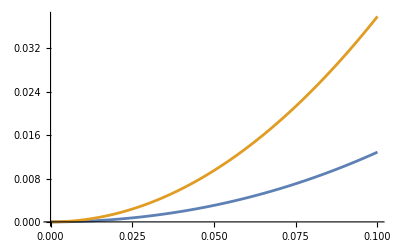

```mathematica
LogLogPlot[{ϵ^2, Norm[Chol[A+ϵ dA]-(L + ϵ dL)],Norm[(L+ϵ dL).(L+ϵ dL)ᵀ-(A+ϵ dA)]},
{ϵ,0.0001,0.1}]
```

## Cholesky Decomposition the Matrix way.

The Cholesky decomposition factorizes an SPD matrix A as
	A=L.Lᵀ
so the product rule gives
	dA=dL.Lᵀ+L.dLᵀ
or in other words 
	L^-1.dA.L^-Τ=L^-1.dL+dLᵀ.L^-T=X+Xᵀ
where X=L^-1.dL.
Since the inverse of a lower triangular matrix is lower triangular and the product of two lower triangular matrices is lower triangular X is lower triangular. Note the diagonal of X is the same as the diagonal of Xᵀ so the diagonal of each is half of the diagonal of L^-1.dA.L.  As always test!

```mathematica
m=4;
{A,dA}=RandomReal[{-1,1},{2,m,m}];A=A.Aᵀ;dA=dA+dAᵀ;
{L,dL}=CholAD[A,dA];
Z=Inverse[L].dA.Inverse[L]ᵀ;
X=LowerTriangularize[Z,-1]+0.5 DiagonalMatrix[Diagonal[Z]];
dLnew=L.X;
Map[MatrixForm,{dL,dLnew}]
```

{(-0.332626 | 0. | 0. | 0.
-0.309564 | 0.500495 | 0. | 0.
0.837806 | 1.25688 | 0.919345 | 0.
-0.498057 | -1.9826 | -3.77688 | 4.21192),(-0.332626 | 0. | 0. | 0.
-0.309564 | 0.500495 | 0. | 0.
0.837806 | 1.25688 | 0.919345 | 0.
-0.498057 | -1.9826 | -3.77688 | 4.21192)}

## Efficiency Discussion

## Break

I have 
	A=Q.H.Qᵀ
so 
	dA = dQ.H.Qᵀ+Q.dH.Qᵀ+Q.H.dQᵀ
so
	Qᵀ.dA.Q = Qᵀ.dQ.H+dH+H.dQᵀ.Q
so with X=Qᵀ.dQ  with Xᵀ=-X and H=H_sym+H_skw we have
(1)	data = X.(H_sym+H_skw)+dH-(H_sym+H_skw).X
transposing gives
	dataᵀ = (H_sym+H_skw)ᵀ.X+dHᵀ+X.(H_sym+H_skw)ᵀ
or equivalently
(2)	dataᵀ = (H_sym-H_skw).X+dHᵀ+X.(H_sym-H_skw)
adding gives
(3)	 data+dataᵀ =
 (H_sym-H_skw).X+dHᵀ+X.(H_sym-H_skw)
+ X.(H_sym+H_skw)+dH-(H_sym+H_skw).X
to get 
	data+dataᵀ =dHᵀ+dH-2H_skw.X-2X.H_skw
	data-dataᵀ =dHᵀ-dH-2H_sym.X-2X.H_sym
Now for a Hessen

```mathematica
m=4; H =2*UpperTriangularize[RandomInteger[{-5,5},{m,m}],-1];
HSym=0.5(H+Hᵀ); HSkew=0.5(H-Hᵀ);
Map[MatrixForm,{H,HSym,HSkew}]
```

{(-10 | 10 | -6 | -4
-2 | 8 | 4 | 0
0 | -2 | 0 | 2
0 | 0 | 0 | -10),(-10. | 4. | -3. | -2.
4. | 8. | 1. | 0.
-3. | 1. | 0. | 1.
-2. | 0. | 1. | -10.),(0. | 6. | -3. | -2.
-6. | 0. | 3. | 0.
3. | -3. | 0. | 1.
2. | 0. | -1. | 0.)}

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];
W1=RandomReal[{-1,1},{m,m}];W1=W1-W1ᵀ;
W2=RandomReal[{-1,1},{m,m}];W2=W2-W2ᵀ;
W3=W1.W2;
MatrixForm[w3]
{Q,H}=HessenbergDecomposition[A];
Map[MatrixForm,{W.H,H.W}]
```

w3

{(1.07962 | 1.07032 | 1.15482 | -0.242459 | -1.60487 | 0.828091 | -1.0757
0.109473 | 0.74163 | -0.844811 | 0.382964 | -1.74454 | -0.894727 | 0.217815
-0.654409 | -0.20834 | 0.0421452 | 0.465015 | -1.58134 | -1.36893 | 0.535768
0.889463 | 0.205277 | -0.220355 | 1.38203 | 0.152169 | 0.465263 | 0.311916
-0.474385 | -0.252664 | 0.950805 | 0.147376 | 0.923596 | 0.456071 | -0.581271
-1.95645 | -2.52901 | 1.44881 | 0.183699 | 0.442251 | -2.6218 | 0.708953
0.504741 | -1.23456 | 1.20897 | -1.47337 | 1.65916 | -0.197172 | -0.768904),(0.31862 | -1.62034 | -0.319742 | -0.29753 | 0.149518 | 0.857271 | 1.01389
-0.610788 | -0.176445 | 0.246265 | 1.54976 | 0.478089 | 1.91503 | 0.488705
-1.18986 | 0.0547577 | 0.0735768 | -0.389204 | 1.37902 | 1.54149 | -0.350043
-0.921132 | -1.13859 | 0.144469 | -0.585696 | -0.421368 | 2.47889 | 1.94515
1.36342 | 0.261935 | 0.649818 | -0.0654842 | -0.0252619 | 0.105183 | -0.448665
0.318199 | 0.684804 | 0.757473 | -1.21248 | -0.76581 | 1.44947 | 1.63714
0.318208 | 0.597131 | -0.0747061 | 0.252309 | 0.493379 | -0.479236 | -0.275946)}

```mathematica
{m,n}={5,3};
H=UpperTriangularize[Array[h,{n+1,n}],-1];
Q=Array[q,{m,n+1}];
dQ=Array[dq,{m,n+1}];
MatrixForm[H]
e[n_]:= SparseArray[{n->1},n]
H⟦All,n⟧-H.e[n]
e[n+1].Qᵀ
```

(h[1,1] | h[1,2] | h[1,3]
h[2,1] | h[2,2] | h[2,3]
0 | h[3,2] | h[3,3]
0 | 0 | h[4,3])

{0,0,0,0}

{q[1,4],q[2,4],q[3,4],q[4,4],q[5,4]}